# Wave Functions for the Morse Potential

C1:
a)

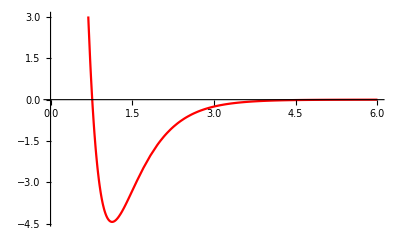

The coordinates at the bottom of the potential read at about -4.44 for the Y intercept, which is consistent with the dept parameter that we used.

```mathematica
V[x_]:=Dpth*(Exp[-2*α*(x-x0)]-2*Exp[-α*(x-x0)])
subs  = {Dpth-> 4.43, α-> 1.9, x0-> 1.13};
Plot[V[x]/.subs,{x,0,6},PlotStyle->Red]
Print["The coordinates at the bottom of the potential read at about -4.44 for the Y intercept, which is consistent with the dept parameter that we used."]
```

b)

α = 1 is plotted in Red, α = 5 is plotted in Blue,α = 10 is plotted in Purple

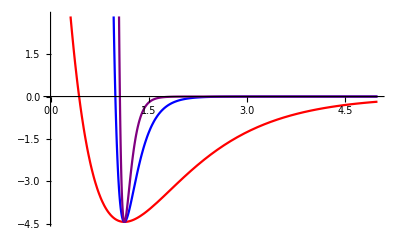

From the Plot one can see that α is a parameter to control the rate that the potential drops and increases once the depth is reached.

```mathematica
Print[" α = 1 is plotted in Red, α = 5 is plotted in Blue,α = 10 is plotted in Purple"]
Plot[{V[x]/.{Dpth->4.43, x0-> 1.13, α-> 1},V[x]/.{Dpth->4.43, x0 -> 1.13, α->5}, V[x]/.{Dpth->4.43,x0->1.13, α->10}},{x,0,5}, PlotStyle->{Red, Blue,Purple}]
Print[" From the Plot one can see that α is a parameter to control the rate that the potential drops and increases once the depth is reached."]
```

C2:
a)

Wavefunction starting at x = 0.5

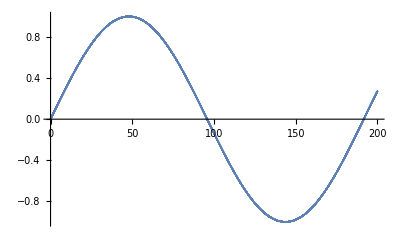

```mathematica
Va[x_]:=4.43*(Exp[-2*1.9*(x-0.5)]-2*Exp[-1.9*(x-0.5)]);
f[x_]=-(0.00215)(Energy-Va[x]);
Subs={Energy->0.5};
xMax=200;
h=0.01;
nSteps=Round[xMax/h];
u[0]=0.5;
u[1]=1;
Do[
u[n+1]=(2+h^2 f[h n])u[n]-u[n-1]/.Subs;
,{n,1,nSteps}]
uRawData=Table[u[n],{n,0,nSteps}];uMax=Max[uRawData];
uData=Table[{h n,u[n]/uMax},{n,0,nSteps}];
Print["Wavefunction starting at x = 0.5"]
uNumPlot=ListPlot[uData]
```

Wavefunction starting a x = 1.5

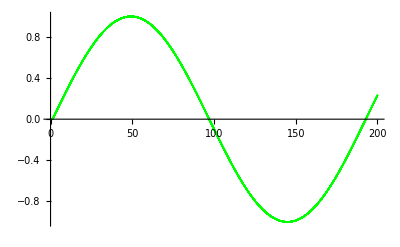

```mathematica
Vaaa[x_]:=4.43*(Exp[-2*1.9*(x-3)]-2*Exp[-1.9*(x-3)]);
faa[x_]=-(0.00215)(energy-Vaaa[x]);
sub={energy->0.5};
xMaxxx=200;
hhh=0.01;
nStepsss=Round[xMaxxx/hhh];
uuu[0]=0;
uuu[1]=0.01;
Do[
uuu[n+1]=(2+hhh^2 faa[hhh n])uuu[n]-uuu[n-1]/.sub;
,{n,1,nStepsss}]
uRawDataaa=Table[uuu[n],{n,0,nStepsss}];uMaxxx=Max[uRawDataaa];
uDataaa=Table[{hhh n,uuu[n]/uMaxxx},{n,0,nStepsss}];
Print["Wavefunction starting a x = 1.5"]
uNumPlott=ListPlot[uDataaa,PlotStyle->Green]
```

b)

Wavefunction starting at x = 0.5 and Energy = 7 eV

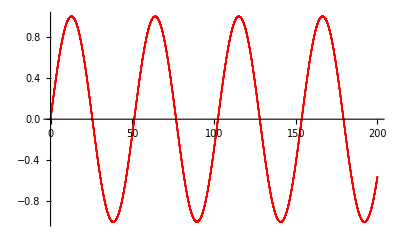

Wavefunctions at same starting point of x = 1.5 but different energy.

Higher energy wavefunction is Red and lower energy wavefunction is Blue.

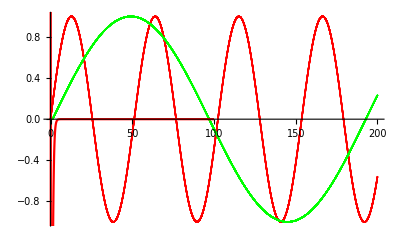

Higher energy results in more ossicaltory behavior

```mathematica
Va[x_]:=4.43*(Exp[-2*1.9*(x-0.5)]-2*Exp[-1.9*(x-0.5)]);
f[x_]=-(0.00215)(Energy-Va[x]);
Subs={Energy->7};
xMax=200;
h=0.01;
nSteps=Round[xMax/h];
u[0]=0.5;
u[1]=1;
Do[
u[n+1]=(2+h^2 f[h n])u[n]-u[n-1]/.Subs;
,{n,1,nSteps}]
uRawData=Table[u[n],{n,0,nSteps}];uMax=Max[uRawData];
uData=Table[{h n,u[n]/uMax},{n,0,nSteps}];
Print["Wavefunction starting at x = 0.5 and Energy = 7 eV"]
uNumPlotEnergy=ListPlot[uData,PlotStyle-> Red]
Print[]
VPlot=Plot[Va[r]/.Subs,{r,0,100},PlotStyle->Red,PlotRange->{-100,100}];
Print["Wavefunctions at same starting point of x = 1.5 but different energy."]
Print["Higher energy wavefunction is Red and lower energy wavefunction is Blue."]
Show[uNumPlotEnergy,uNumPlott,VPlot]
Print["Higher energy results in more ossicaltory behavior"]
```

c) 
The wavelength is shorter in the regions of the potential well since the kinetic energy of the wavefunction is lower at that potential.

C3:
a)

```mathematica
Va[x_]:=4.43*(Exp[-2*1.9*(x-3)]-2*Exp[-1.9*(x - 3)]);
f[x_]=-(0.00215)(Q-Va[x]);
Subs={Q->Qnew};
Qnew = 0.7;
rMin=0.9;
rMid=1.15;
rMax=1.8;
VPlot=Plot[Va[r]/.Subs,{r,0,rMax},PlotStyle->Red,PlotRange->{-1,0}]
h=0.001;
nSteps=Round[(rMax-rMin)/h];
nStepsL=Round[(rMid-rMin)/h];
nStepsR=Round[(rMax-rMid)/h];
uL[0]=0;
uL[1]=0.01;
Do[
uL[n+1]=(2+h^2 f[rMin+h n])uL[n]-uL[n-1]/.Subs;
,{n,1,nStepsL}]
uR[0]=0;
uR[1]=0.01;
Do[
uR[n+1]=(2+h^2 f[rMax-h n])uR[n]-uR[n-1]/.Subs;
,{n,1,nStepsR}]
Do[u[n]=If[n<nStepsL,uL[n]/uL[nStepsL],uR[nSteps-n]/uR[nStepsR]],{n,0,nSteps}];
uData=Table[{rMin+h n,u[n]/4+Q/.Subs},{n,0,nSteps}];
uNumPlot=ListPlot[uData];

EnePlot=Plot[Q/.Subs,{r,rMin,rMax},PlotStyle->Black];
Show[VPlot,EnePlot,uNumPlot]
```

b)